```mathematica
ClearAll["Global`*"];
NotebookFind[SelectedNotebook[],"Output",All,CellStyle];FrontEndExecute[FrontEndToken["Clear"]];
NotebookDelete@Cells@MessagesNotebook[];

category="H3";

Get[NotebookDirectory[]<>"Functions.m"];
Get[NotebookDirectory[]<>"TubeFunctions.m"];

Switch[category,
"Z2",
Get[NotebookDirectory[]<>"VecZ2/Z2Data.m"];
Get[NotebookDirectory[]<>"VecZ2/MData.m"];
Get[NotebookDirectory[]<>"VecZ2/TubeDataZ2M.m"];
,
"VecS3",
Get[NotebookDirectory[]<>"VecS3/VecS3Data.m"];
Get[NotebookDirectory[]<>"VecS3/MData.m"];
Get[NotebookDirectory[]<>"VecS3/TubeDataVecS3M.m"];
,
"RepS3",
Get[NotebookDirectory[]<>"RepS3/RepS3Data.m"];
Get[NotebookDirectory[]<>"RepS3/MData.m"];
Get[NotebookDirectory[]<>"RepS3/TubeDataRepS3M.m"];
,
"H3",
Get[NotebookDirectory[]<>"Haagerup/H3Data.m"];
Get[NotebookDirectory[]<>"Haagerup/MData.m"];
Get[NotebookDirectory[]<>"Haagerup/TubeDataH3M.m"];
]
```

### Input category

Fusion rules input category

```mathematica
TableForm[Table[Sum[V[a,b][c]objNames[c],{c,obs}],{a,obs},{b,obs}],TableHeadings->{objNames[#]&/@obs,objNames[#]&/@obs}]
```

| 1 | α | α^2 | ρ | α ρ | α^2 ρ
1 | 1 | α | α^2 | ρ | α ρ | α^2 ρ
α | α | α^2 | 1 | α ρ | α^2 ρ | ρ
α^2 | α^2 | 1 | α | α^2 ρ | ρ | α ρ
ρ | ρ | α^2 ρ | α ρ | 1+ρ+α ρ+α^2 ρ | α^2+ρ+α ρ+α^2 ρ | α+ρ+α ρ+α^2 ρ
α ρ | α ρ | ρ | α^2 ρ | α+ρ+α ρ+α^2 ρ | 1+ρ+α ρ+α^2 ρ | α^2+ρ+α ρ+α^2 ρ
α^2 ρ | α^2 ρ | α ρ | ρ | α^2+ρ+α ρ+α^2 ρ | α+ρ+α ρ+α^2 ρ | 1+ρ+α ρ+α^2 ρ

#### Dimensions input category

```mathematica
dim[#]&/@obs
dtot[]^2
```

{1,1,1,1/2 (3+√13),1/2 (3+√13),1/2 (3+√13)}

3/2 (13+3 √13)

#### Frobenius-Schur indicators

```mathematica
κ[#]&/@obs
```

{1,1,1,1,1,1}

#### Unitary fusion input category?

```mathematica
NpentagonQ&&NunitaryQ(*Being checked numerically, can check exactly by removing leading 'N'*)
```

True

### Module category

Fusion rules module

```mathematica
TableForm[Table[Sum[W[a,b][c]MNames[c],{c,obsM}],{a,obs},{b,obsM}],TableHeadings->{objNames[#]&/@obs,MNames[#]&/@obsM}]
```

| Γ | α Γ | α^2 Γ | Λ
1 | Γ | α Γ | α^2 Γ | Λ
α | α Γ | α^2 Γ | Γ | Λ
α^2 | α^2 Γ | Γ | α Γ | Λ
ρ | α Γ+α^2 Γ+Λ | Γ+α Γ+Λ | Γ+α^2 Γ+Λ | Γ+α Γ+α^2 Γ+Λ
α ρ | Γ+α^2 Γ+Λ | α Γ+α^2 Γ+Λ | Γ+α Γ+Λ | Γ+α Γ+α^2 Γ+Λ
α^2 ρ | Γ+α Γ+Λ | Γ+α^2 Γ+Λ | α Γ+α^2 Γ+Λ | Γ+α Γ+α^2 Γ+Λ

#### Dimensions module objects

```mathematica
dimM[#]&/@obsM
```

{√(4+√13),√(4+√13),√(4+√13),√(3/2 (5+√13))}

#### Unitary module category?

```mathematica
NpentagonMQ&&NunitaryMQ(*Being checked numerically, can check exactly by removing leading 'N'*)
```

True

### Endomorphism category

#### Dimension of tube algebra

```mathematica
Length[pictureBasis[]]
```

555

#### Dimension of representations

```mathematica
dimVS[#]&/@reps
```

{4,9,13,17}

#### Fusion rules

```mathematica
TableForm[
Table[PrintTemporary[a⊗b];
Sum[fusionMultiplicity[a, b][c] c, {c, reps}],
 {a, reps}, {b, reps}],
TableHeadings->{reps,reps}]
```

| 1 | μ | η | ν
1 | 1 | μ | η | ν
μ | μ | 1+ν | η+ν | η+μ+ν
η | η | η+ν | 1+η+μ+ν | η+μ+2 ν
ν | ν | η+μ+ν | η+μ+2 ν | 1+2 η+μ+2 ν

#### Dimensions output category

```mathematica
dimEnd[#]&/@reps
dtotEnd[]^2
```

{1,1/2 (1+√13),1/2 (3+√13),1/2 (5+√13)}

3/2 (13+3 √13)

#### Isometric embedding?

```mathematica
NisometricQ
```

{True}

#### Visualization of F-matrices for End_C[M]

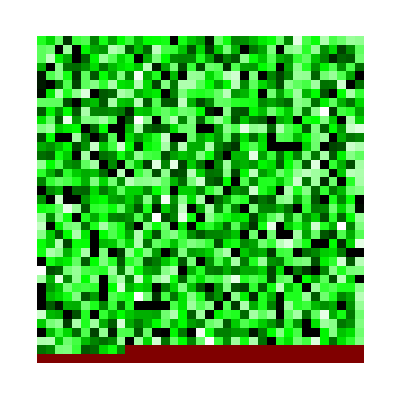

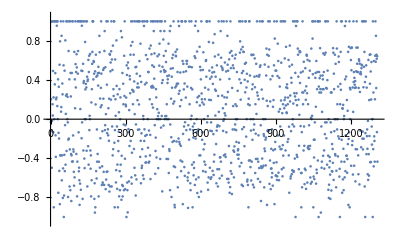

```mathematica
ArrayPlot[ArrayReshape[RandomSample[(NFEnds+1)/2],Ceiling[Sqrt[Length[NFEnds]]]{1,1},∞],ColorFunction-> (Blend[{White,Green,Black},#]&),Frame->False,ColorFunctionScaling->False]
ListPlot[RandomSample[NFEnds],PlotRange->{-1.05,1.05}]
```

#### Frobenius-Schur indicators

```mathematica
NκEnd[#]&/@reps
```

{1.,1.,1.,1.}

#### Unitary fusion category?

```mathematica
NpentagonEndQ&&NunitaryEndQ
```

True